Trying to derive eq. 2 from “Precision interferometric measurements of mirror birefringence in high-finesse optical resonators”

```mathematica
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
```

```mathematica
Ein={√(f1 a1),√(f2 a2)ⅇ^(ⅈ(ϕ-ωb t))};
(*arbitrary electric field input to the cavity in terms of cavity polarization bases H,V. ωb is the pol. mode splitting*)
Iin=conj[Ein].Ein;(*using 1/2 ce0=1*)
vPA={Cos[γ],-Sin[γ]};
PA=Outer[Times,vPA,vPA];(*projective measurement along a basis vector V'*)
Iout=conj[(PA.Ein)].(PA.Ein)//FullSimplify;
"intensity after polarization analyzer. γ is angle between cavity slow axis and the polarization analyzer"
ⅇ^(-t/τ)*Iout
```

intensity after polarization analyzer. γ is angle between cavity slow axis and the polarization analyzer

ⅇ^(-t/τ) (a1 f1 Cos[γ]^2+a2 f2 Sin[γ]^2-√(a1 f1) √(a2 f2) Cos[ϕ-t ωb] Sin[2 γ])

Specific case for circularly polarized input state:

```mathematica
Ein={√(f1 a1),√(f2 a2)ⅇ^(ⅈ(ϕ-ωb t))}/.{ϕ->π/2,a1->1/2,a2->1/2,f1->1/2,f2->1/2};
(*arbitrary electric field input to the cavity in terms of cavity polarization bases H,V. ωb is the pol. mode splitting*)
Iin=conj[Ein].Ein;(*using 1/2 ce0=1*)
vPA={Cos[γ],-Sin[γ]};
PA=Outer[Times,vPA,vPA];(*projective measurement along a basis vector V'*)
Iout=conj[(PA.Ein)].(PA.Ein)//FullSimplify;
"intensity after polarization analyzer. γ is angle between cavity slow axis and the polarization analyzer"
ⅇ^(-t/τ)*Iout/Iin
```

intensity after polarization analyzer. γ is angle between cavity slow axis and the polarization analyzer

1/2 ⅇ^(-t/τ) (1-2 Cos[γ] Sin[γ] Sin[t ωb])

The expression above agrees with equation 3 for ϕ=pi/2 up to a factor of 1/2.  I can’t seem to get it to go away. Might be their error, or they normalized in a different way.

```mathematica
τ *2π*13.8
```

1.23869

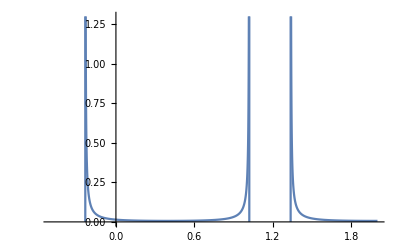

```mathematica
κ=2π*70;
τ=2π/κ;
Plot[τ/(1+ τ wb Sin[4θ])/.{wb->2π*13.8},{θ,-0.5,2},PlotRange->{0,1.3}]
```

Spoof the data from Joseph Schupp thesis (Blatt group)

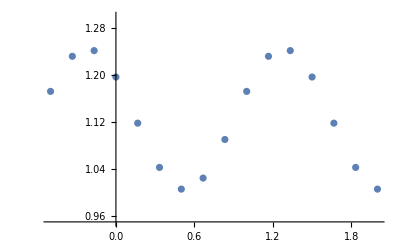

```mathematica
data=Table[{θ,0.12Sin[(2π)/1.5 θ+2.5]+1.125},{θ,Range[-0.5,2,0.5/3]}];
ListPlot[data,PlotRange->{0.95,1.3}]
```

```mathematica
Clear[τ,wb];
model=τ/(1+ τ wb Sin[4(θ-α)]);
FindFit[data,model,{α,wb,τ},θ]
```

{α→0.127738,wb→0.094394,τ→1.11588}

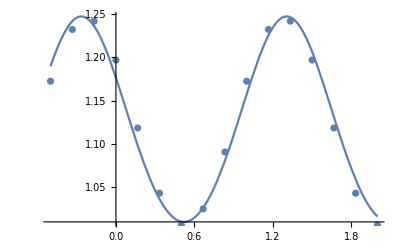

```mathematica
Show[Plot[model/.%,{θ,-0.5,2}],ListPlot[data,PlotRange->{0.95,1.3}]]
```

```mathematica
(2π)/1.11
```

5.66053